```mathematica
Quit[];
```

```mathematica
ScalarF0[m_,s_]:=-(2 √(4 m^2-s))/(√s)ArcTan[(√s)/(√(4 m^2-s))];
ScalarF1[m_,s_]:=(2 √(4 m^2-s))/(√s)(ArcTan[-(√s)/(√(4 m^2-s))]+π);
ScalarFPrime1[m_,s_]:=-1/s+(4 m^2)/(√(4 m^2-s) s^(3/2))(ArcTan[(√s)/(√(4 m^2-s))]-π);
ScalarP[s_,m_,μ_,RScalar_]:=Abs[1-Im[μ^2]RScalar ScalarFPrime1[m,μ^2]/Im[ScalarF1[m,μ^2]]]/(s-μ^2-Im[μ^2]RScalar(ScalarF0[m,s]-ScalarF1[m,μ^2])/Im[ScalarF1[m,μ^2]]);
```

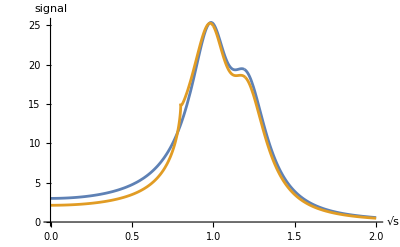

```mathematica
Plot[{Abs[ScalarP[p^2,0.4,1-0.14ⅈ,0]+1.1ScalarP[p^2,0.4,1.2-0.15ⅈ,0]]^2,Abs[ScalarP[p^2,0.4,1-0.14ⅈ,0.5]+1.1ScalarP[p^2,0.4,1.2-0.15ⅈ,0.6]]^2},{p,0,2},AxesLabel->{Sqrt[s],signal},MaxRecursion->15]
```